```mathematica
(*No-Feedback parameters for Fig 1C, Fig 2A, 
as specified in Table S2(1) of the Supplement*)
p0A=0.25;q0A=0.2;p1A=0.3;q1A=0.1;
v0A=0.5;v1A=1;d2A=0.05;
d0A=0.1;d2A=1;d1A=0.5;

(*Equations for No-Feedback, Equation (1) in Main Paper*)
equA = (x0'[t]==(p0A-q0A)*v0A*x0[t]-d0A*x0[t]);
equB = (x1'[t]==(1-p0A+q0A)*v0A*x0[t]+
(p1A-q1A)*v1A*x1[t]-d1A*x1[t]);
equC = (x2'[t]==(1-p1A+q1A)*v1A*x1[t]-d2A*x2[t]);

(*Simulation of No-Feedback Results*)
initNumCells1C = 1.5*10^5;
initNumCells2A = 1.5;
noFeedbackResults1C = NDSolveValue[{equA,equB,equC,
x0[0]==initNumCells1C,x1[0]==initNumCells1C,
x2[0]==initNumCells1C},{x0,x1,x2},{t,0,20}];
noFeedbackResults2A= NDSolveValue[{equA,equB,equC,
x0[0]==initNumCells2A,x1[0]==initNumCells2A,
x2[0]==initNumCells2A},{x0,x1,x2},{t,0,20}];
noFeedbackNumCells1C[t_]:=noFeedbackResults1C[[1]][t]+
noFeedbackResults1C[[2]][t]+
noFeedbackResults1C[[3]][t];
noFeedbackNumCells2A[tt_]:=noFeedbackResults2A[[1]][tt]+
noFeedbackResults2A[[2]][tt]+
noFeedbackResults2A[[3]][tt];
```

```mathematica
(*Parameters for Type I Feedback in Fig 1C, 2A*)
p0B=0.5;q0B=0.2;p1B=0.5;q1B=0.1;
v0B=0.5;v1B=1;d2B=0.05;d0B=0.1;
d1B=0.5;d2B=1;beta0B=2*10^-11;
beta1B=3*10^-12; tau=2;

(*Equations for Type I Feedback, specified as Equation S2 in Supplement*)
equ0=(x0'[t]==(p0B-q0B)(v0B/(1+beta0B*(x2[t-tau])^2))*x0[t]-
d0B*x0[t]);
equ1 = (x1'[t]==(1-p0B+q0B)*(v0B/(1+beta0B*(x2[t-tau])^2))*x0[t]+
(p1B-q1B)(v1B/(1+beta1B*(x2[t-tau])^2))*x1[t]-d1B*x1[t]);
equ2 = (x2'[t]==(1-p1B+q1B)(v1B/(1+beta1B*(x2[t-tau])^2))*x1[t]-
d2B*x2[t]);

(*Simulation of Type I Feedback Results for 1C, 2A. 
Can Use initial number of cells parameter specified previously*)
typeIfeedbackResults1C = NDSolveValue[{equ0,equ1,equ2,
x0[0]==initNumCells1C,x1[0]==initNumCells1C,
x2[0]==initNumCells1C},{x0,x1,x2},{t,0,20}];
typeIfeedbackResults2A = NDSolveValue[{equ0,equ1,equ2,
x0[0]==initNumCells2A,x1[0]==initNumCells2A,
x2[0]==initNumCells2A},{x0,x1,x2},{t,0,20}];
typeIfeedbackNumCells1C[t_]:=typeIfeedbackResults1C[[1]][t]+
typeIfeedbackResults1C[[2]][t]+typeIfeedbackResults1C[[3]][t];
typeIfeedbackNumCells2A[t_]:=typeIfeedbackResults2A[[1]][t]+
typeIfeedbackResults2A[[2]][t]+typeIfeedbackResults2A[[3]][t];
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

```mathematica
(*Parameters for Type II Feedback in Fig 1C, 2A*)
p0C=0.5; q0C=0.2; p1C=0.5; q1C=0.1;v0C=0.5; 
v1C=1; d2C=0.05; d0C=0.1;d1C=0.5; d2C=1; tau=2; 
gamma10C=5*10^-14; gamma20C = 7 * 10^-15; 
gamma11C = 6*10^-13; gamma21C = 2*10^-15;

(*Equations for Type II Feedback, specified as Equation S3 in Supplement*)
equ3 = (x0'[t]==(p0C/(1+gamma10C*(x2[t-tau])^2) - 
q0C/(1+gamma20C*(x2[t-tau])^2))*v0C*x0[t]-d0C*x0[t]);
equ4 = (x1'[t]==(p0/(1+gamma10C*(x2[t-tau])^2) - 
q0C/(1+gamma20C*(x2[t-tau])^2))*v0C*x0[t] + 
(p0C/(1+gamma11C*(x2[t-tau])^2) -
 q0C/(1+gamma21C*(x2[t-tau])^2))*v1C*x1[t]-
d1C*x1[t]);
equ5 = (x2'[t]==(1-p1C/(1+gamma11C*(x2[t-tau])^2) 
+ q1C/(1+gamma21C*(x2[t-tau])^2))*v1C*x1[t]-
d2C*x2[t]);

(*Simulation of Type II Feedback Results for 1C, 2A. 
Can Use initial number of cells parameter specified previously*)
typeIIfeedbackResults1C = NDSolveValue[{equ3,equ4,equ5,
x0[0]==initNumCells1C,x1[0]==initNumCells1C,
x2[0]==initNumCells1C},{x0,x1,x2},{t,0,20}];
typeIIfeedbackResults2A = NDSolveValue[{equ3,equ4,equ5,
x0[0]==initNumCells2A,x1[0]==initNumCells2A,
x2[0]==initNumCells2A},{x0,x1,x2},{t,0,20}]
typeIIfeedbackNumCells1C[t_]:=typeIIfeedbackResults1C[[1]][t]+
typeIIfeedbackResults1C[[2]][t]+typeIIfeedbackResults1C[[3]][t];
typeIIfeedbackNumCells2A[t_]:=typeIIfeedbackResults2A[[1]][t]+
typeIIfeedbackResults2A[[2]][t]+typeIIfeedbackResults2A[[3]][t];
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

NDSolveValue::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolveValue[{x0'[t]==-0.1 x0[t]+0.5 x0[t] (-0.2/(1+(7 x2[-2+t]^2)/1000000000000000)+0.5/(1+x2[-2+t]^2/20000000000000)),x1'[t]==-0.5 x1[t]+0.5 x0[t] (-0.2/(1+(7 x2[-2+t]^2)/1000000000000000)+p0/(1+x2[-2+t]^2/20000000000000))+x1[t] (-0.2/(1+x2[-2+t]^2/500000000000000)+0.5/(1+(3 x2[-2+t]^2)/5000000000000)),x2'[t]==x1[t] (1+0.1/(1+x2[-2+t]^2/500000000000000)-0.5/(1+(3 x2[-2+t]^2)/5000000000000))-x2[t],x0[0]==1.5,x1[0]==1.5,x2[0]==1.5},{x0,x1,x2},{t,0,20}]

```mathematica
(*Parameters for Type I and II Feedback in Fig 1C, 2A*)
p0D=0.5; q0D=0.2 ; p1D=0.5; q1D=0.1;v0D=0.5; v1D=1; 
d2D=0.05; d0D=0.1;d1D=0.5; d2D=1; tau=2; gamma10D=10^-14; 
gamma20D = 10^-16; gamma11D = 10^-13; gamma21D = 10^-15;
beta0D=8*10^-12; beta1D=4*10^-13;

(*Equations for Type I and II Feedback, specified as Equation S4 in Supplement*)
equ6 = (x0'[t]==(p0D/(1+gamma10D*(x2[t-tau])^2) - 
q0D/(1+gamma20D*(x2[t-tau])^2))*
(v0D/(1+beta0D*(x2[t-tau])^2))*x0[t]-
d0D*x0[t]);
equ7 = (x1'[t]==(1-p0D/(1+gamma10D*(x2[t-tau])^2) +
 q0D/(1+gamma20D*(x2[t-tau])^2))*
(v0D/(1+beta0D*(x2[t-tau])^2))*x0[t]+
(p1D/(1+gamma11D*(x2[t-tau])^2) + 
q1D/(1+gamma21D*(x2[t-tau])^2))*
(v1D/(1+beta1D*(x2[t-tau])^2))*x1[t]-d1D*x1[t]);
equ8 = (x2'[t]==(1-p1D/(1+gamma11D*(x2[t-tau])^2) 
+ q1D/(1+gamma21D*(x2[t-tau])^2))*
(v1D/(1+beta1D*(x2[t-tau])^2))*x1[t]-
d2D*x2[t]);

(*Simulation of Type I and II Feedback Results for 1C, 2A. 
Can Use initial number of cells parameter specified previously*)
typeIandIIfeedbackResults1C = NDSolveValue[{equ6,equ7,equ8,
x0[0]==initNumCells1C,x1[0]==initNumCells1C,x2[0]==initNumCells1C},{x0,x1,x2},{t,0,20}];
typeIandIIfeedbackResults2A = NDSolveValue[{equ6,equ7,equ8,
x0[0]==initNumCells2A,x1[0]==initNumCells2A,x2[0]==initNumCells2A},{x0,x1,x2},{t,0,20}]
typeIandIIfeedbackNumCells1C[t_]:=typeIandIIfeedbackResults1C[[1]][t]+
typeIandIIfeedbackResults1C[[2]][t]+typeIandIIfeedbackResults1C[[3]][t];
typeIandIIfeedbackNumCells2A[t_]:=typeIandIIfeedbackResults2A[[1]][t]+
typeIandIIfeedbackResults2A[[2]][t]+typeIandIIfeedbackResults2A[[3]][t];
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}

NDSolveValue::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

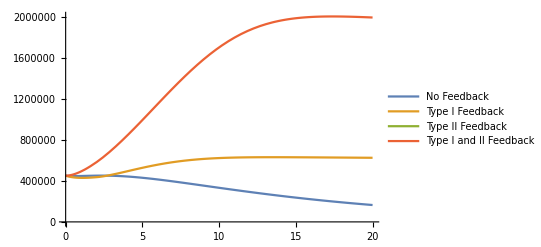

```mathematica
(*Figure 1C Attempt*)
Plot[{noFeedbackNumCells1C[t],typeIfeedbackNumCells1C[t],
typeIIfeedbackNumCells1C[t],typeIandIIfeedbackNumCells1C[t]},
{t,0,20},PlotLegends->{
"No Feedback","Type I Feedback",
"Type II Feedback","Type I and II Feedback"}]
```

NDSolveValue::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

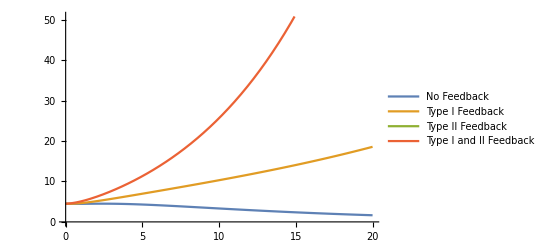

```mathematica
(*Figure 2A Attempt*)
Plot[{noFeedbackNumCells2A[t],typeIfeedbackNumCells2A[t],
typeIIfeedbackNumCells2A[t],typeIandIIfeedbackNumCells2A[t]},
{t,0,20},PlotLegends->{"No Feedback","Type I Feedback",
"Type II Feedback","Type I and II Feedback"}]
```

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 120.}}, <>],InterpolatingFunction[{{0., 120.}}, <>],InterpolatingFunction[{{0., 120.}}, <>]}

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{InterpolatingFunction[{{0., 15.}}, <>],InterpolatingFunction[{{0., 15.}}, <>],InterpolatingFunction[{{0., 15.}}, <>]}

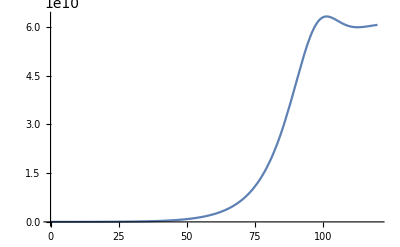

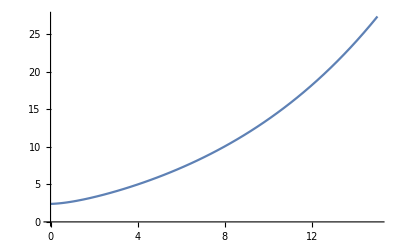

```mathematica
(*Figure 1D, 2B Attempt, Type I and II Feedback with Different Parameters*)
(*These are the parameters, as specified in Table S2(2) of the Supplement*)
p0E=0.5; q0E=0.2; p1E=0.5;q1E=0.1; v0E=0.5; v1E=1; 
d2E=0.05;d0E=0.1; d1E=0.5; d2E=1;
tau=2; gamma10E=10^-23; gamma20E = 2*10^-24; 
gamma11E = 4*10^-22; gamma21E =5* 10^-23;
beta0E=8*10^-27; beta1E=4*10^-27;

(*Initial number of cells for 1D, 2B*)
initNumCells1D = 5 * 10^5;
initNumCells2B = 0.8;

(*Type I and II Feedback Equations, as specified in Equation S4 of the Supplement*)
equ10 = (x0'[t]==(p0E/(1+gamma10E*(x2[t-tau])^2) - 
q0E/(1+gamma20E*(x2[t-tau])^2))*
(v0E/(1+beta0E*(x2[t-tau])^2))*x0[t]-
d0E*x0[t]);
equ11 = (x1'[t]==(1-p0E/(1+gamma10E*(x2[t-tau])^2) + 
q0E/(1+gamma20E*(x2[t-tau])^2))*
(v0E/(1+beta0E*(x2[t-tau])^2))*x0[t]+
(p1E/(1+gamma11E*(x2[t-tau])^2) +
 q1E/(1+gamma21E*(x2[t-tau])^2))*
(v1E/(1+beta1E*(x2[t-tau])^2))*x1[t]-d1E*x1[t]);
equ12 = (x2'[t]==(1-p1E/(1+gamma11E*(x2[t-tau])^2) + 
q1E/(1+gamma21E*(x2[t-tau])^2))*
(v1E/(1+beta1E*(x2[t-tau])^2))*x1[t]-d2E*x2[t]);

(*Simulation of Type I and II Feedback for 1D, 2B*)
fig1DsimResults1D = NDSolveValue[{equ10,equ11,equ12,x0[0]==initNumCells1D,x1[0]==initNumCells1D,x2[0]==initNumCells1D},{x0,x1,x2},{t,0,120}]
fig1DsimResults2B = NDSolveValue[{equ10,equ11,equ12,x0[0]==initNumCells2B,x1[0]==initNumCells2B,x2[0]==initNumCells2B},{x0,x1,x2},{t,0,15}]
typeIandIIfeedbackNumCells1D[t_]:=fig1DsimResults1D[[1]][t]+fig1DsimResults1D[[2]][t]+fig1DsimResults1D[[3]][t];
typeIandIIfeedbackNumCells2B[t_]:=fig1DsimResults2B[[1]][t]+fig1DsimResults2B[[2]][t]+fig1DsimResults2B[[3]][t];

(*Make the Plots for 1D, then 2B*)
Plot[typeIandIIfeedbackNumCells1D[t],{t,0,120}]
Plot[typeIandIIfeedbackNumCells2B[t],{t,0,15}]
```